```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
CTri={0,0};
```

```mathematica
RT=2;
```

```mathematica
Coord={{1,2},{2,3},{2,7},{3,8},{4,9},{5,11},{10,10},{7,8},{4,4},{2,1},{1,2}};
```

```mathematica
(* Points *)
```

```mathematica
P1={Blue,PointSize->0.03,Point[Coord]}
```

{RGBColor[0, 0, 1],PointSize→0.03,Point[{{1,2},{2,3},{2,7},{3,8},{4,9},{5,11},{10,10},{7,8},{4,4},{2,1},{1,2}}]}

```mathematica
(* Check *)
```

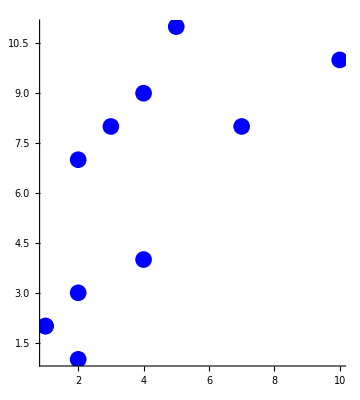

```mathematica
ShowPoint = Graphics[P1, Axes->True]
```

```mathematica
(* Arrows, Note Flatten[XXX,1] *)
```

```mathematica
LofAr1T=Table[{Coord[[i]],Coord[[i+1]]},{i,Length[Coord]-1}]
```

{{{1,2},{2,3}},{{2,3},{2,7}},{{2,7},{3,8}},{{3,8},{4,9}},{{4,9},{5,11}},{{5,11},{10,10}},{{10,10},{7,8}},{{7,8},{4,4}},{{4,4},{2,1}},{{2,1},{1,2}}}

```mathematica
LofAr1=Flatten[LofAr1T,1]
```

{{1,2},{2,3},{2,3},{2,7},{2,7},{3,8},{3,8},{4,9},{4,9},{5,11},{5,11},{10,10},{10,10},{7,8},{7,8},{4,4},{4,4},{2,1},{2,1},{1,2}}

```mathematica
ArY = {Red,Arrow[LofAr1T]}
```

{RGBColor[1, 0, 0],Arrow[{{{1,2},{2,3}},{{2,3},{2,7}},{{2,7},{3,8}},{{3,8},{4,9}},{{4,9},{5,11}},{{5,11},{10,10}},{{10,10},{7,8}},{{7,8},{4,4}},{{4,4},{2,1}},{{2,1},{1,2}}}]}

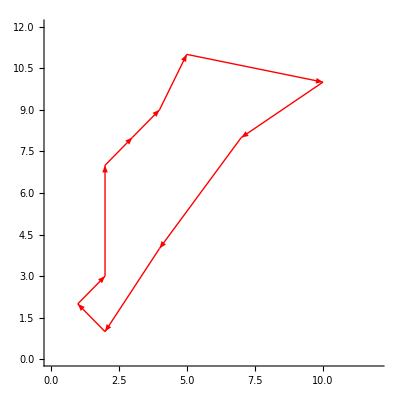

```mathematica
G2 =Graphics[ArY, Axes->True,PlotRange-> {{0,12},{0,12}}]
```

```mathematica
(* Show the points and the arrows *)
```

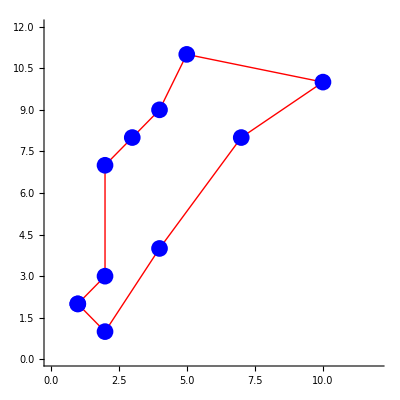

```mathematica
ShowArrowAll=Show[G2,ShowPoint]
```

```mathematica
Tri=RegularPolygon[CTri,RT,4]
```

RegularPolygon[{0,0},2,4]

```mathematica
(* Check *)
```

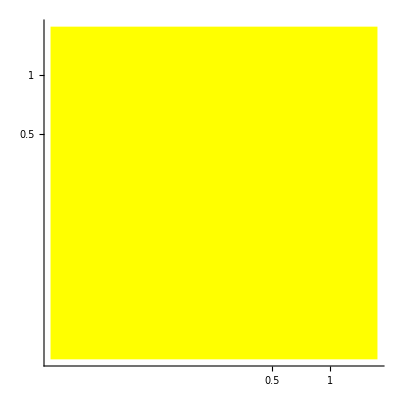

```mathematica
G5 =Graphics[{Yellow,Tri},Ticks -> {{0.5,1,1.5},{0.5,1,1.5,2}},Axes -> True]
```

```mathematica
(* Move the Square using the TranslationTransform along the set of points (point by point) using the index Coord[[i]] *)
```

```mathematica
Trans2[i_]:=GeometricTransformation[{Yellow,Tri},TranslationTransform[Coord[[i]]]]
```

```mathematica
(* Design animation *)
```

```mathematica
ArrowTri[i_]:=Graphics[{Trans2[i] },Axes->True,AxesOrigin->{0,0},PlotRange->{{0,12},{0,12}}];
```

```mathematica
ShowAll[i_]:=Show[ArrowTri[i],ShowArrowAll];
```

```mathematica
Manipulate[ShowAll[i],{i,1,Length[Coord],1}]
```

```mathematica
OctaMagen={Magenta,RegularPolygon[CTri,RT,8]}
```

{RGBColor[1, 0, 1],RegularPolygon[{0,0},2,8]}

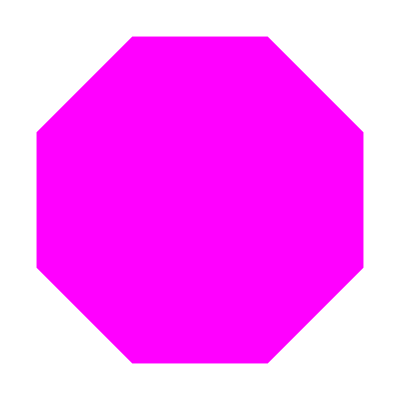

```mathematica
Graphics[OctaMagen]
```

```mathematica
Trans3[i_,a_]:=GeometricTransformation[OctaMagen,Composition[TranslationTransform[Coord[[i]]],RotationTransform[3*a]]];
```

```mathematica
ObjectPen[i_,a_]:=Graphics[{Trans3[i,a]},Axes->True,PlotRange->{{0,12},{0,12}},AxesOrigin->{0,0}];
```

```mathematica
ShowAllAllAll[i_,a_]:=Show[ObjectPen[i,a],ShowArrowAll]
```

```mathematica
Manipulate[ShowAllAllAll[i,a],{i,1,Length[Coord],1},{a,0,2*Pi}]
```